# Analytical Solution for Exponential potential.

## Library stuff:

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files\Microsoft Visual Studio\2022\Community,CompilerName→Automatic}}

## Jost Function:

```mathematica
Jost[p_]:= Gamma[1-2*I*p]*BesselJ[-2*I*p,2];
```

```mathematica
Jost[-0.6*I]
```

3.40466+0. ⅈ

```mathematica
Jost[-0.4*I]
```

-2.2088+0. ⅈ

```mathematica
Gamma[1-2*I*(0.6*I)]
```

1.1018+0. ⅈ

```mathematica
Gamma[1-2*I*(-0.6*I)]
```

-5.82115-7.12885×10^-16 ⅈ

```mathematica
BesselJ[-2*I*(-0.6*I),2]
```

-0.584878+7.16269×10^-17 ⅈ

```mathematica
HankelH1[0,2]//N
```

0.223891+0.510376 ⅈ

```mathematica
FullSimplify[1 + 1/π Integrate[HankelH1[0,k]/(k - I*(-0.4*I)),{k,0.5,∞}]]
```

(π+∫_0.5^∞ HankelH1[0,k]/(-0.4+k)ⅆk)/π

```mathematica
Integrate[HankelH1[0,k]/(k - I*(-1.2*I)),{k,0.5,∞}]
```

Integrate::idiv: Integral of HankelH1[0,k]/(-1.2+k) does not converge on {0.5,∞}.

∫_0.5^∞ HankelH1[0,k]/((-1.2+0. ⅈ)+k)ⅆk

## Scattering functions:

```mathematica
PCOT[p_]:= ((Jost[-p]-Jost[p])/(2*I*p*Jost[p]) )^-1+I*p;
T[p_]:=-4*π*(Jost[-p]-Jost[p])/(2*I*p*Jost[p]);
S[p_]:= Jost[-p]/Jost[p];
phaseshift[p_]:=1/(2*I)Log[Jost[-p]/Jost[p]];
```

## Potential:

```mathematica
eps = 0;
V1[p_,k_]=(-8*π)/((p^2+k^2+2*p*k + 1 + I*eps)(p^2+k^2-2*p*k + 1 + I*eps));
```

## T-Matrix:

```mathematica
TMAT = Table[T[P],{P,p}]//N;
Plot[{Re[T[Sqrt[E1]]], Im[T[Sqrt[E1]]]},{E1,-5,1},PlotLegends->{Real(T),Imag(T)},AxesLabel->{Energy,}]
```

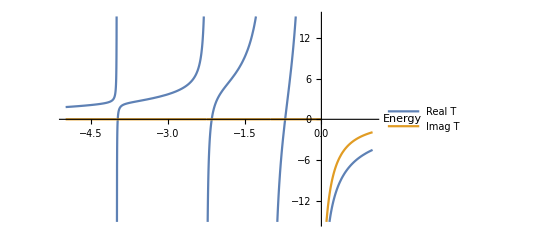

## Poles of the potential:

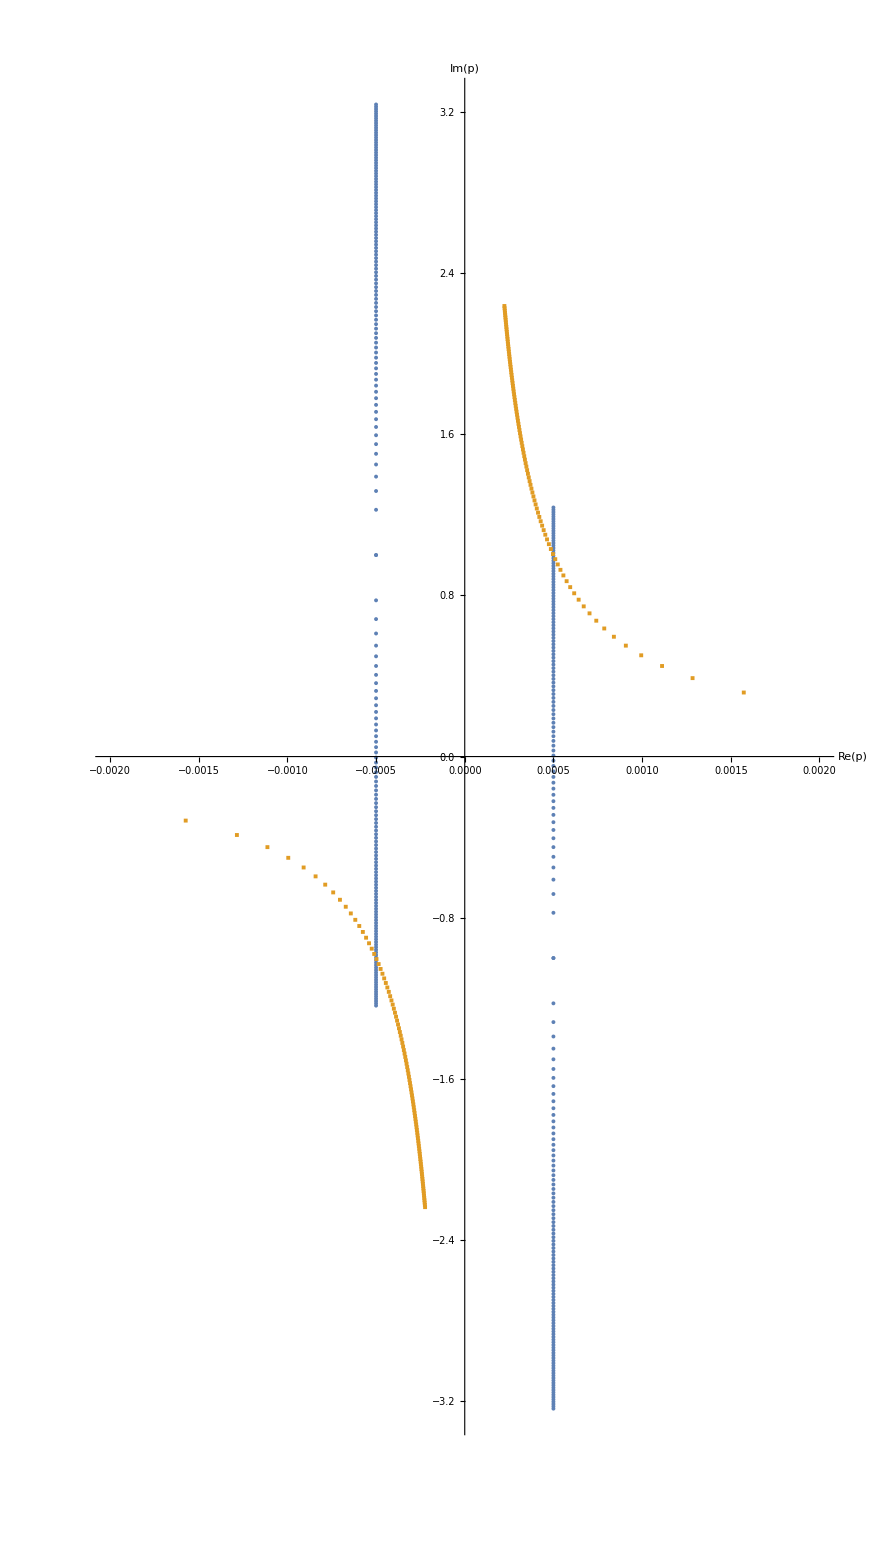

```mathematica
solution[q0_] := FullSimplify[p/.Solve[1/V[q0 ,p]==0,p]]//N;
solution1[q0_] := FullSimplify[p/.Solve[-p^2 + (q0)^2 + I*eps==0,p]]//N;
q = Array[Sqrt[#]&,100,{0,-5}]//N;
Solutions = Table[solution[q0],{q0,q}]//Flatten;
Solutions1 = Table[solution1[q0],{q0,q}]//Flatten;
ComplexListPlot[{Solutions,Solutions1},PlotMarkers->{Automatic, Tiny},AxesLabel->{Re[p],Im[p]}]
```

## Residue of VGV:

```mathematica
solution[q0_] = FullSimplify[p/.Solve[1/V[q0,p]==0,p]]//N;
pole = solution[q0];
resvgv := (2*π*I/(2*π^2))Residue[V[q0,k] k^2/(q0^2- k^2)*V[k,q0],{k,pole[[3]]}];
Eg = Array[# &,20,{-1.1,-3}]//N;
res = resvgv/.{q0->Sqrt[Eg]};
For[i = 1, i < 21, i++, Print["Energy"->Eg[[i]]"," "Residue"-> res[[i]]]];
```

Energy→-1.1 , Residue→-53.6624+0. ⅈ

Energy→-1.2 , Residue→-23.5765+0. ⅈ

Energy→-1.3 , Residue→-14.1103+0. ⅈ

Energy→-1.4 , Residue→-9.65804+0. ⅈ

Energy→-1.5 , Residue→-7.14237+0. ⅈ

Energy→-1.6 , Residue→-5.55825+0. ⅈ

Energy→-1.7 , Residue→-4.48552+0. ⅈ

Energy→-1.8 , Residue→-3.71986+0. ⅈ

Energy→-1.9 , Residue→-3.15105+0. ⅈ

Energy→-2. , Residue→-2.71491+0. ⅈ

Energy→-2.1 , Residue→-2.37183+0. ⅈ

Energy→-2.2 , Residue→-2.09619+0. ⅈ

Energy→-2.3 , Residue→-1.87075+0. ⅈ

Energy→-2.4 , Residue→-1.68354+0. ⅈ

Energy→-2.5 , Residue→-1.52604+0. ⅈ

Energy→-2.6 , Residue→-1.392+0. ⅈ

Energy→-2.7 , Residue→-1.27679+0. ⅈ

Energy→-2.8 , Residue→-1.17688+0. ⅈ

Energy→-2.9 , Residue→-1.08955+0. ⅈ

Energy→-3. , Residue→-1.01267+0. ⅈ

## Next order in Born series:

We want to go to next order in Born series. So we have (∫_)^∞(V(q0,k)k^2)/(q0^2 - k^2)(∫_)^∞(V(k,q)V(q,q0)q^2)/(q0^2 - q^2)ⅆqⅆk to calculate. 
We start with I_1 = (∫_)^∞(V(k,q)V(q,q0)q^2)/(q0^2 - q^2)ⅆq, which has a pole at q→ - i + q0.  Therefore we write  (∫_)^∞(V(k,q)V(q,q0)q^2)/(q0^2 - q^2)ⅆq - Res[I_1]

```mathematica
poles = Solve[1/FullSimplify[V[k,q] q^2/(q0^2- q^2)*V[q,q0]]==0,q]
```

{{q→-ⅈ-k},{q→ⅈ-k},{q→-ⅈ+k},{q→ⅈ+k},{q→-ⅈ-q0},{q→ⅈ-q0},{q→-q0},{q→q0},{q→-ⅈ+q0},{q→ⅈ+q0}}

```mathematica
int = Integrate[V[k,q] q^2/(q0^2- q^2)*V[q,q0],{q,0,∞}];
res = 2*π*I*Residue[V[k,q] q^2/(q0^2- q^2)*V[q,q0],{q,q/.poles[[9]]}];
I1 =FullSimplify[ (1/(2*π^2))*(int - res)]
```

ConditionalExpression[-(8 ⅈ π (-ⅈ-2 q0+k (ⅈ+k+q0) (3 ⅈ+k+q0)))/(k (k-q0) (2 ⅈ+k-q0) (k+q0) (-ⅈ+k+q0) (ⅈ+k+q0) (2 ⅈ+k+q0) (ⅈ+2 q0)), Im[k]>1&&Im[q0]>1]

Now we need to perform the outer integral and see for poles.

```mathematica
poles1 = Solve[1/FullSimplify[V[q0,k] k^2/(q0^2- k^2)*-(8 ⅈ π (-ⅈ-2 q0+k (ⅈ+k+q0) (3 ⅈ+k+q0)))/(k (k-q0) (2 ⅈ+k-q0) (k+q0) (-ⅈ+k+q0) (ⅈ+k+q0) (2 ⅈ+k+q0) (ⅈ+2 q0))]==0,k]
```

{{k→-ⅈ-q0},{k→-ⅈ-q0},{k→ⅈ-q0},{k→ⅈ-q0},{k→-2 ⅈ-q0},{k→-q0},{k→-q0},{k→q0},{k→q0},{k→-ⅈ+q0},{k→ⅈ+q0},{k→-2 ⅈ+q0}}

```mathematica
int1 = Integrate[V[q0,k] k^2/(q0^2- k^2)*-(8 ⅈ π (-ⅈ-2 q0+k (ⅈ+k+q0) (3 ⅈ+k+q0)))/(k (k-q0) (2 ⅈ+k-q0) (k+q0) (-ⅈ+k+q0) (ⅈ+k+q0) (2 ⅈ+k+q0) (ⅈ+2 q0)),{k,0,∞}];
res1 = 2*π*I*Residue[V[q0,k] k^2/(q0^2- k^2)*-(8 ⅈ π (-ⅈ-2 q0+k (ⅈ+k+q0) (3 ⅈ+k+q0)))/(k (k-q0) (2 ⅈ+k-q0) (k+q0) (-ⅈ+k+q0) (ⅈ+k+q0) (2 ⅈ+k+q0) (ⅈ+2 q0)),{k,k/.poles1[[10]]}];
I2 =FullSimplify[ (1/(2*π^2))*(int1 - res1)]
```

ConditionalExpression[(2 (-6 ⅈ (-9-22 q0^2+64 q0^4+32 q0^6)+π (27+q0 (27 ⅈ+q0 (338+q0 (93 ⅈ+16 q0 (54+q0 (36 ⅈ+q0 (63+5 q0 (3 ⅈ+4 q0)))))))))+ⅈ q0 (6 (-2+9 q0^2+72 q0^4+16 q0^6) ArcTan[2/q0]+12 (1+q0^2) (-19+56 q0^2+16 q0^4) ArcTan[q0]-108 ⅈ (Log[-q0]-Log[q0])+q0 (3 (-171+q0 (-25 ⅈ+2 q0 (-47+4 q0 (13 ⅈ+2 q0 (4+q0 (3 ⅈ+2 q0)))))) Log[-q0]-3 (171+q0 (-25 ⅈ+2 q0 (335+4 q0 (13 ⅈ+2 q0 (48+q0 (3 ⅈ+14 q0)))))) Log[q0]+32 (1+q0^2) (17+22 q0^2+8 q0^4) Log[1+q0^2]+(1+4 q0^2) (-31+22 q0^2+8 q0^4) Log[4+q0^2])))/(3 q0^2 (1+q0^2) (1+4 q0^2)^3 (9+4 q0^2)), (-1<Im[q0]<0||0<Im[q0]<1)&&Re[q0]==0]

```mathematica
I3 = 1/(3 q0^2 (1+q0^2) (1+4 q0^2)^3 (9+4 q0^2))(2 (-6 ⅈ (-9-22 q0^2+64 q0^4+32 q0^6)+π (27+q0 (27 ⅈ+q0 (338+q0 (93 ⅈ+16 q0 (54+q0 (36 ⅈ+q0 (63+5 q0 (3 ⅈ+4 q0)))))))))+ⅈ q0 (6 (-2+9 q0^2+72 q0^4+16 q0^6) ArcTan[2/q0]+12 (1+q0^2) (-19+56 q0^2+16 q0^4) ArcTan[q0]-108 ⅈ (Log[-q0]-Log[q0])+q0 (3 (-171+q0 (-25 ⅈ+2 q0 (-47+4 q0 (13 ⅈ+2 q0 (4+q0 (3 ⅈ+2 q0)))))) Log[-q0]-3 (171+q0 (-25 ⅈ+2 q0 (335+4 q0 (13 ⅈ+2 q0 (48+q0 (3 ⅈ+14 q0)))))) Log[q0]+32 (1+q0^2) (17+22 q0^2+8 q0^4) Log[1+q0^2]+(1+4 q0^2) (-31+22 q0^2+8 q0^4) Log[4+q0^2])));
Eg = Array[# &,20,{-1.1,-3}]//N;
B2 = Table[I3/.{q0->Sqrt[l]},{l,Eg}];
For[i = 1, i < 21, i++, Print["Energy"->Eg[[i]]"," "Secon order correction"-> B2[[i]]]];
```

Energy→-1.1 , Secon order correction→56.7702+12.2845 ⅈ

Energy→-1.2 , Secon order correction→25.6762+5.17332 ⅈ

Energy→-1.3 , Secon order correction→15.5482+2.8783 ⅈ

Energy→-1.4 , Secon order correction→10.6461+1.80767 ⅈ

Energy→-1.5 , Secon order correction→7.81627+1.21938 ⅈ

Energy→-1.6 , Secon order correction→6.00776+0.863513 ⅈ

Energy→-1.7 , Secon order correction→4.77187+0.633805 ⅈ

Energy→-1.8 , Secon order correction→3.88585+0.478302 ⅈ

Energy→-1.9 , Secon order correction→3.22722+0.36908 ⅈ

Energy→-2. , Secon order correction→2.72348+0.290056 ⅈ

Energy→-2.1 , Secon order correction→2.32919+0.231461 ⅈ

Energy→-2.2 , Secon order correction→2.01459+0.187105 ⅈ

Energy→-2.3 , Secon order correction→1.75947+0.152926 ⅈ

Energy→-2.4 , Secon order correction→1.54969+0.126176 ⅈ

Energy→-2.5 , Secon order correction→1.37509+0.104954 ⅈ

Energy→-2.6 , Secon order correction→1.22821+0.0879113 ⅈ

Energy→-2.7 , Secon order correction→1.10349+0.0740738 ⅈ

Energy→-2.8 , Secon order correction→0.996682+0.0627266 ⅈ

Energy→-2.9 , Secon order correction→0.904528+0.053336 ⅈ

Energy→-3. , Secon order correction→0.824468+0.0454981 ⅈ

## Second order poles:

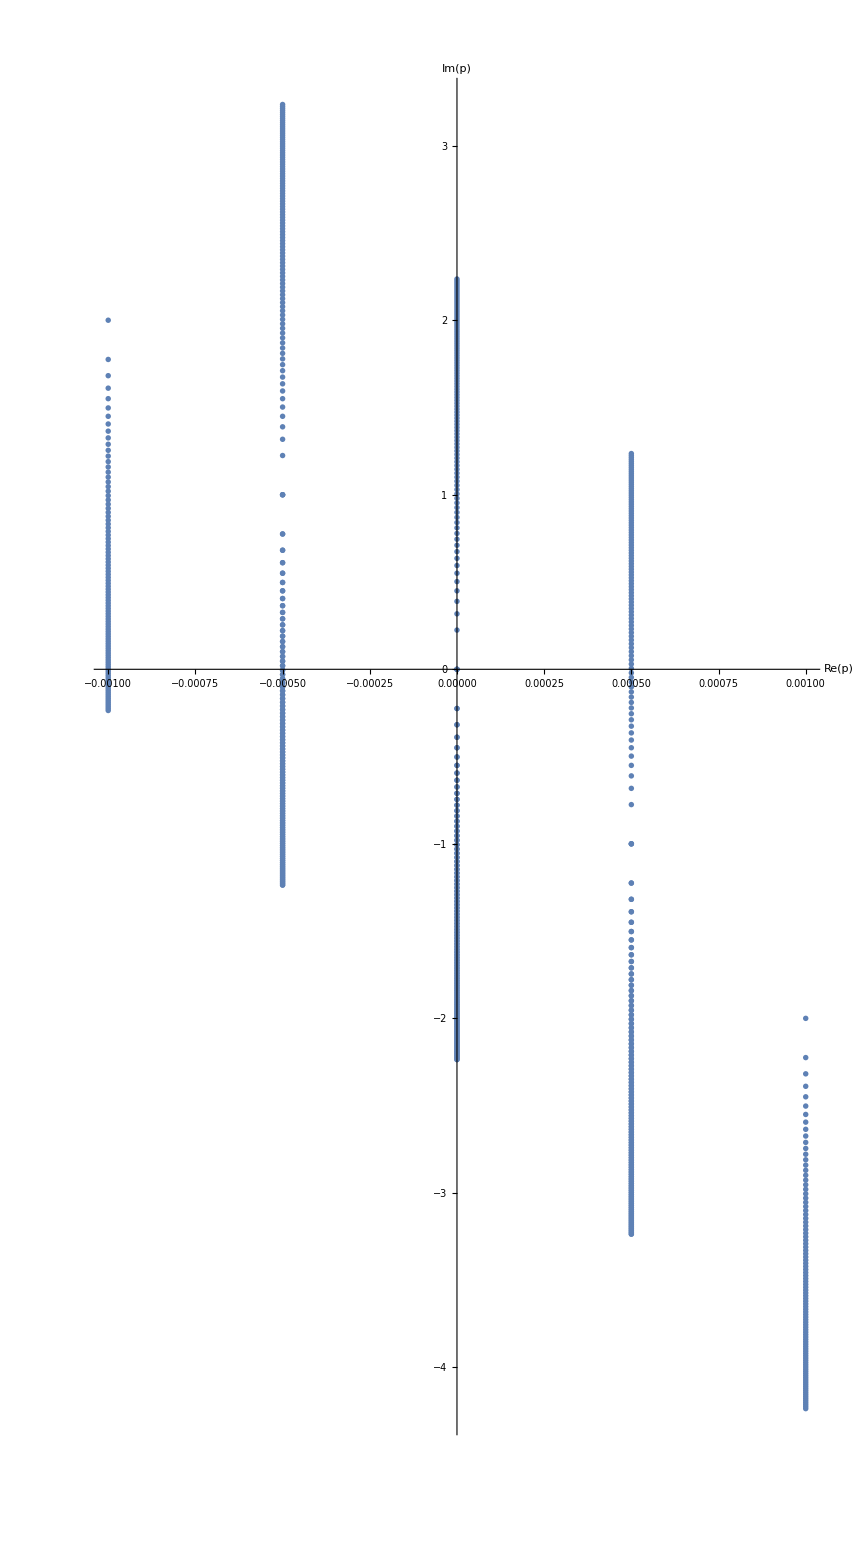

```mathematica
poles22[q0_] = k/.Solve[1/FullSimplify[V[q0,k] k^2/(q0^2- k^2)*(2000000 ⅈ π ((1000+ⅈ)+1000 (k+q0) (k+4 q0)))/(k q0 (k+q0) ((1000+ⅈ)+4000 q0^2) ((1000+ⅈ)+250 (k+q0)^2) ((1000+ⅈ)+1000 (k+q0)^2))]==0,k]//N;
p1 = Array[Sqrt[#]&,100,{-1,-5}]//N;
Solutions22 = Table[poles22[q0],{q0,p1}]//Flatten;
ComplexListPlot[Solutions22,AxesLabel->{Re[p],Im[p]}]
```

# Numerical solution for Exponential potential.

## Numerical functions:

```mathematica
(*Potential*)
V = Compile[{{p,_Complex},{k,_Complex}},Module[{m=1,g=1},(-8*π*m*g)/((p^2+k^2+2*p*k + m^2)(p^2+k^2-2*p*k + m^2))]];
(*T-matrix (half-offshell)= T(k,q0;q0^2)*)
Module[{n,xa},
n = 100;
xa = GaussianQuadratureWeights[n,0,1];
Ths = Compile[{{k,_Complex}},Module[{xa1,scale,p,wa1,factor,matrixA,matrixV},
scale = 1;
factor = (1/(2*π^2));
xa1 = xa[[All,1]];
wa1 = xa[[All,2]];
p = scale*(-1 + 1/xa1);
matrixV = Table[V[p[[i]],k],{i,1,n}];
matrixA = Table[-factor*scale*wa1[[j]]/xa1[[j]]^2*p[[j]]^2*V[p[[i]],p[[j]]]/(k^2 - p[[j]]^2),{i,1,n},{j,1,n}] + IdentityMatrix[n];
Inverse[matrixA].matrixV
]]];
(*T-matrix (full-onshell)= T(q0,q0;q0^2) works only for q0^2< -1*)

Module[{n,xa},
n = 100;
xa = GaussianQuadratureWeights[n,0,1];

Tos = Compile[{{k,_Complex}},Module[{xa1,scale,p,wa1,factor,MatrixT,matrixV,sample,weights,points,T},
scale = 1;
factor = (1/(2*π^2));
xa1 = xa[[All,1]];
wa1 = xa[[All,2]];
p = scale*(-1 + 1/xa1);
T = Ths[k];
MatrixT = Sum[factor*scale*wa1[[j]]/xa1[[j]]^2*p[[j]]^2*V[k,p[[j]]]/(k^2 - p[[j]]^2)*T[[j]],{j,1,n}];
matrixV = V[k,k];
SetPrecision[MatrixT + matrixV,12]
]]];

Tplot = Compile[{},Module[{E1,points,data},E1 = Array[#&,100,{-0.99,-0.1}];
points = Table[Tos[Sqrt[En]],{En,E1}];
data = Transpose@{E1,points}]];
```

Compile::part: Part specification xa$4385⟦All,1⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::part: Part specification GaussianQuadratureWeights[100,0,1]⟦All,1⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::part: Part specification xa$4385⟦All,2⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

General::stop: Further output of Compile::part will be suppressed during this calculation.

Compile::part: Part specification xa$4415⟦All,1⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::part: Part specification GaussianQuadratureWeights[100,0,1]⟦All,1⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::part: Part specification xa$4415⟦All,2⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

General::stop: Further output of Compile::part will be suppressed during this calculation.

## Contour

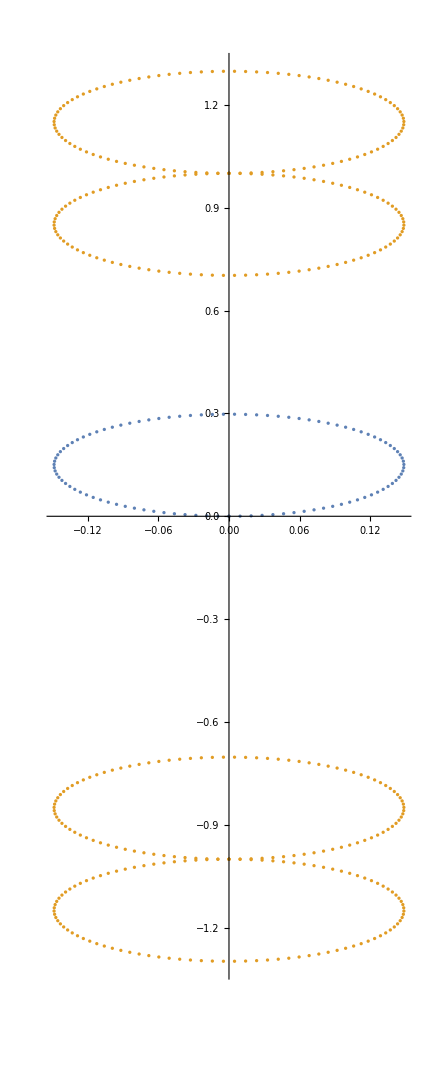

```mathematica
contour[r_,δ_,ϕ_] = (r - 1 + δ)*I*(1 - Exp[-I*ϕ]);
q[r_,δ_] = Array[contour[r,δ,#]&,100,{0,2π}];
solution[q0_] = p/.Solve[FullSimplify[1/V1[p,q0]] == 0,p];
pole = Table[solution[q0],{q0,q[Sqrt[1.1],0.1]}]//Flatten;
ComplexListPlot[{q[Sqrt[1.1],0.1],pole}]
```

```mathematica
solution[q0] = p/.Solve[FullSimplify[1/V1[p,q0]] == 0,p]
```

{-ⅈ-q0,ⅈ-q0,-ⅈ+q0,ⅈ+q0}

```mathematica
Manipulate[Show[ParametricPlot[ReIm[k],{k,0,3},PlotRange->{{-3,3},{-3,3}}],ParametricPlot[ReIm[(r - 1 + δ)*I*(1-Exp[-I*ϕ])],{ϕ,0,2*π},PlotStyle->Orange],
Graphics[{{Red,PointSize[0.02],Point[ReIm[q0]]},{Blue,Point[ReIm[-q0]]},{Black,Point[ReIm[ⅈ-q0]]},{Gray,Point[ReIm[-ⅈ-q0]]},
{Green,Point[ReIm[ⅈ+q0]]},{Pink,Point[ReIm[-ⅈ+q0]]}},PlotRange->{{-3,3},{-3,3}}]]/.q0->r*I,{{r,1.2},0,2},{δ,0,1}]
```

```mathematica
Sqrt[-1.1] - (r - 1 + δ)*I*(1-Exp[-I*ϕ])/.{r->-I*Sqrt[-1.1],ϕ->π,δ->0.19}
```

0.+0.571191 ⅈ

```mathematica
Sqrt[-1.2] - (r - 1 + δ)*I*(1-Exp[-I*ϕ])/.{r->-I*Sqrt[-1.2],ϕ->π,δ->0.15}
```

0.+0.604555 ⅈ

```mathematica
Sqrt[-1.3] - (r - 1 + δ)*I*(1-Exp[-I*ϕ])/.{r->-I*Sqrt[-1.3],ϕ->π,δ->0.10}
```

0.+0.659825 ⅈ

```mathematica
Sqrt[-1.4] - (r - 1 + δ)*I*(1-Exp[-I*ϕ])/.{r->-I*Sqrt[-1.4],ϕ->π,δ->0.06}
```

0.+0.696784 ⅈ

```mathematica
Sqrt[-1.5] - (r - 1 + δ)*I*(1-Exp[-I*ϕ])/.{r->-I*Sqrt[-1.5],ϕ->π,δ->0.02}
```

0.+0.735255 ⅈ

```mathematica
-I*Sqrt[-1.1] - 1 + 0.19
```

0.238809+0. ⅈ

```mathematica
-I*Sqrt[-1.2] - 1 + 0.15
```

0.245445+0. ⅈ

```mathematica
-I*Sqrt[-1.3] - 1 + 0.10
```

0.240175+0. ⅈ

```mathematica
-I*Sqrt[-1.4] - 1 + 0.06
```

0.243216+0. ⅈ

```mathematica
-I*Sqrt[-1.5] - 1 + 0.02
```

0.244745+0. ⅈ

```mathematica
Sqrt[-1.6]
```

0.+1.26491 ⅈ

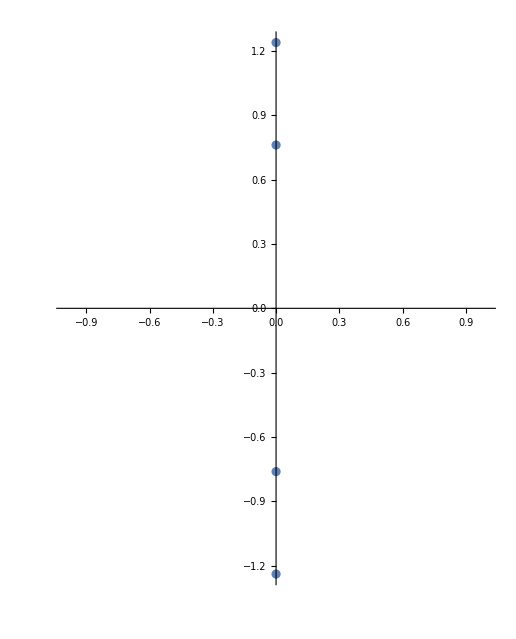

```mathematica
Func[r_,δ_] = p/.Solve[1/V1[(r - 1 + δ)*I,p]==0,p];
ComplexListPlot[Func[Sqrt[1.1],0.19]]
```